### Start choosing the example:

```mathematica
t=7;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->5}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.040573 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.119267,Null}

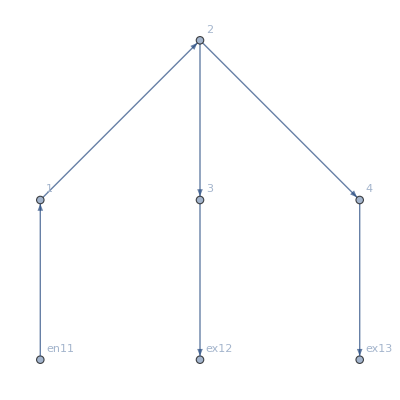

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0.,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→8.,u39→6.,u40→6.,u41→5.,u42→5.,u43→8.,u44→6.,u45→5.,u46→5.,u47→5.,u48→5.,u49→8.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→6.75229,u39→5.70576,u40→5.70576,u41→5.,u42→5.,u43→6.75229,u44→5.70576,u45→5.,u46→5.,u47→5.,u48→5.,u49→6.75229|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.71948×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→6.82592,u39→5.72685,u40→5.72685,u41→5.,u42→5.,u43→6.82592,u44→5.72685,u45→5.,u46→5.,u47→5.,u48→5.,u49→6.82592|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.71028×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.71028×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→6.99482,u39→5.77321,u40→5.77321,u41→5.,u42→5.,u43→6.99482,u44→5.77321,u45→5.,u46→5.,u47→5.,u48→5.,u49→6.99482|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.43896×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→7.79269,u39→5.9592,u40→5.9592,u41→5.,u42→5.,u43→7.79269,u44→5.9592,u45→5.,u46→5.,u47→5.,u48→5.,u49→7.79269|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[2.71948×10^-15,ComplexInfinity]

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→8.,u39→6.,u40→6.,u41→5.,u42→5.,u43→8.,u44→6.,u45→5.,u46→5.,u47→5.,u48→5.,u49→8.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.69185×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.69185×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→8.53675,u39→6.0941,u40→6.0941,u41→5.,u42→5.,u43→8.53675,u44→6.0941,u45→5.,u46→5.,u47→5.,u48→5.,u49→8.53675|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.0229×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14578×10^-15

«6 more identical outputs»

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→9.92172,u39→6.27899,u40→6.27899,u41→5.,u42→5.,u43→9.92172,u44→6.27899,u45→5.,u46→5.,u47→5.,u48→5.,u49→9.92172|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10(*,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)*)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.53329×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.53329×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→10.7031,u39→6.35738,u40→6.35738,u41→5.,u42→5.,u43→10.7031,u44→6.35738,u45→5.,u46→5.,u47→5.,u48→5.,u49→10.7031|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.81446×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.62458×10^-16

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→13.5434,u39→6.55247,u40→6.55247,u41→5.,u42→5.,u43→13.5434,u44→6.55247,u45→5.,u46→5.,u47→5.,u48→5.,u49→13.5434|>

```mathematica
<|j14->2.,j15->2.,j16->0.,j17->2.,j18->0.,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->2.,jt29->0.,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->2.,jt35->0.,jt36->0.,jt37->0.,u38->13.990914203088625,u39->7.,u40->7.,u41->5.,u42->5.,u43->13.990914203088625,u44->7.,u45->5.,u46->2.009085796911375,u47->5.,u48->5.,u49->13.990914203088625|>;
```

```mathematica
<|j14->2.,j15->1.000000000000022,j16->0.999999999999978,j17->1.000000000000022,j18->0.999999999999978,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->1.000000000000022,jt29->0.999999999999978,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->1.000000000000022,jt35->0.,jt36->0.999999999999978,jt37->0.,u38->13.543381675652178,u39->6.552467472563553,u40->6.552467472563553,u41->5.,u42->5.,u43->13.543381675652178,u44->6.552467472563553,u45->4.999999999999999,u46->5.,u47->5.,u48->5.,u49->13.543381675652178|>
```

```mathematica
<|j14->2.,j15->1.0000000000000002,j16->0.9999999999999998,j17->1.0000000000000002,j18->0.9999999999999998,j19->2.,j20->0.,j21->0.,j22->0.,j23->0.,j24->0.,j25->0.,jt26->0.,jt27->2.,jt28->1.0000000000000002,jt29->0.9999999999999998,jt30->0.,jt31->0.,jt32->0,jt33->0.,jt34->1.0000000000000002,jt35->0.,jt36->0.9999999999999998,jt37->0.,u38->13.543381675652178,u39->6.552467472563554,u40->6.552467472563554,u41->5.,u42->5.,u43->13.543381675652178,u44->6.552467472563554,u45->5.000000000000001,u46->5.,u47->5.,u48->5.,u49->13.543381675652178|>;
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94896×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.94896×10^-17

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→16.5708,u39→6.6767,u40→6.6767,u41→5.,u42→5.,u43→16.5708,u44→6.6767,u45→5.,u46→5.,u47→5.,u48→5.,u49→16.5708|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.17756×10^-17

<|j14→2.,j15→1.,j16→1.,j17→1.,j18→1.,j19→2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→2.,jt28→1.,jt29→1.,jt30→0.,jt31→0.,jt32→0,jt33→0.,jt34→1.,jt35→0.,jt36→1.,jt37→0.,u38→23.1999,u39→6.82668,u40→6.82668,u41→5.,u42→5.,u43→23.1999,u44→6.82668,u45→5.,u46→5.,u47→5.,u48→5.,u49→23.1999|>